```mathematica
Clear[w,Rl,g,Lp,Ls,Cp,Cs,x];
Lp=Ls=52×10^-6;
Cp=Cs=220×10^-9;
Uin=24;
fr=47050;
k=0.157;
M=√(Lp×Ls)×k;
Rp=0.11;
Rs=0.11;
w=x*fr;
s=2*π*w*I;
R1=Rp+(s*Lp+1/(s*Cp));
R2=Rs+Rl+(s*Ls+1/(s*Cs));
Rf=(s*M)^2/R2;
g=(s×M)*Rl/(R1×R2+(s×M)^2);

g=Sqrt[ComplexExpand[Re[FullSimplify[g]]]^2+ComplexExpand[Im[FullSimplify[g]]]^2]
a=0.8;
b=0.7;

p1=Plot[Evaluate@Table[g,{Rl,2.4,2.4,1}],{x,0.9,1.35},
PlotRange->{0,1.3},
Frame->True,
FrameLabel->{Style["(:5f52:4e00:5316:9891:7387f)_s/Hz",Black],Style["(:7535:538b:589e:76cag)_V",Black]},
PlotLegends->Placed[{"   R_L=2.4Ω(仿真)"},{a,b}],
(*PlotLabel->Style["(:4e0d:540c:8d1f:8f7d:7535:963bR)_L下，(:7535:538b:589e:76caG)_u(:4e0e:9891:7387f)_s的关系",Black,Bold],*)
PlotStyle->{Red,Thick}];
p2=Plot[Evaluate@Table[g,{Rl,8,8,1}],{x,0.9,1.35},
PlotRange->{0,5},
Frame->True,
FrameLabel->{Style["(:9891:7387f)_s/Hz",Black],Style["(:7535:538b:589e:76caG)_u",Black]},
PlotLegends->Placed[{"   R_L=8Ω(仿真)"},{a,b}],
(*PlotLabel->Style["(:4e0d:540c:8d1f:8f7d:7535:963bR)_L下，(:7535:538b:589e:76caG)_u(:4e0e:9891:7387f)_s的关系",Black,Bold],*)
PlotStyle->{Purple,Thick}];

Show[p1,p2,PlotRange->All]
```

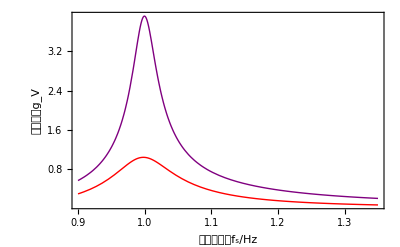

```mathematica
√(((0.+0. ⅈ)-(0.03454755497044291 Rl x^4)/((0.-0.2200481208308465 x-1.0002187310493023 Rl x+0.21999999999999997 x^3+1. Rl x^3)^2+(15.37916676838948+x (-0.007155662445887553 Rl x+x (-30.75239432833622+15.751356475007652 x^2)))^2)-(0.1570343407747405 Rl^2 x^4)/((0.-0.2200481208308465 x-1.0002187310493023 Rl x+0.21999999999999997 x^3+1. Rl x^3)^2+(15.37916676838948+x (-0.007155662445887553 Rl x+x (-30.75239432833622+15.751356475007652 x^2)))^2)+(0.03454 Rl x^6)/((0.-0.2200481208308465 x-1.0002187310493023 Rl x+0.21999999999999997 x^3+1. Rl x^3)^2+(15.37916676838948+x (-0.007155662445887553 Rl x+x (-30.75239432833622+15.751356475007652 x^2)))^2)+(0.15700000000000003 Rl^2 x^6)/((0.-0.2200481208308465 x-1.0002187310493023 Rl x+0.21999999999999997 x^3+1. Rl x^3)^2+(15.37916676838948+x (-0.007155662445887553 Rl x+x (-30.75239432833622+15.751356475007652 x^2)))^2))^2+((0.+0. ⅈ)-(2.414529182637149 Rl x^3)/((0.-0.2200481208308465 x-1.0002187310493023 Rl x+0.21999999999999997 x^3+1. Rl x^3)^2+(15.37916676838948+x (-0.007155662445887553 Rl x+x (-30.75239432833622+15.751356475007652 x^2)))^2)+(4.828125909548787 '\'\x^5)/((0.-0.2200481208308465 x-1.0002187310493023 Rl x+0.21999999999999997 x^3+1. Rl x^3)^2+(15.37916676838948+x (-0.007155662445887553 Rl x+x (-30.75239432833622+15.751356475007652 x^2)))^2)+(0.001123439004004346 Rl^2 x^5)/((0.-0.2200481208308465 x-1.0002187310493023 Rl x+0.21999999999999997 x^3+1. Rl x^3)^2+(15.37916676838948+x (-0.007155662445887553 Rl x+x (-30.75239432833622+15.751356475007652 x^2)))^2)-(2.472962966576202 Rl x^7)/((0.-0.2200481208308465 x-1.0002187310493023 Rl x+0.21999999999999997 x^3+1. Rl x^3)^2+(15.37916676838948+x (-0.007155662445887553 Rl x+x (-30.75239432833622+15.751356475007652 x^2)))^2))^2)
```